```mathematica
Ndet[G_]:=G/(π (1.75*2.54/2)^2)/1200
```

```mathematica
Nbeam = ((1.75*2.54/2)/(2*(69.1-4.05-44.3-1.1)))^2*10^-6*3.7*10^10
```

118.331

```mathematica
Ntgts=3.67*6.02*10^23*64*2.54/149.89424
```

2.39602×10^24

```mathematica
dΩ[θ1_, θ2_] := 2 π Sin[(θ1+θ2)/2](θ2-θ1)
```

```mathematica
θ[E_]:=ArcCos[1-(1/(1-(E/662))-1)/(662/511)]
```

```mathematica
σ[g_,E1_,E2_]:=Ndet[g]/(Nbeam Ntgts dΩ[θ[E1],θ[E2]])
```

```mathematica
σ[34044,300,400]
```

1.88103×10^-27

```mathematica
Solve[θ[x]==π/2, x]
```

{{x→438244/1173}}

```mathematica
σ[8380,350,375]
```

1.76914×10^-27

```mathematica
Theoreticalσ(Θ_):=((0.5 (2.8/10^13)^2 (cos^2(Θ)+1)) ((4/511 662 sin^4(Θ/2)+1)/((2/511 662 sin^2(Θ/2)+1) (cos^2(Θ)+1))+1))/((2/511 662 sin^2(Θ/2)+1)^2)
```

```mathematica
Theoreticalσ[dΩ[θ[300],θ[400]]]
```

1.12985×10^-26

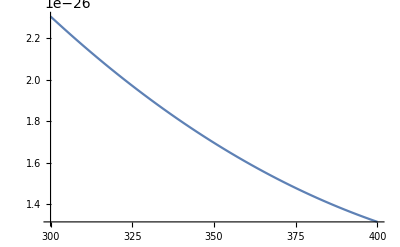

```mathematica
Plot[Theoreticalσ[θ[x]], {x,300,400}]
```

```mathematica
dΩ[θ[300], θ[400]]
```

2 π (ArcCos[-7739/43361]-ArcCos[21586/59911]) Sin[1/2 (ArcCos[-7739/43361]+ArcCos[21586/59911])]

```mathematica
dΩ[0,π]
```

2 π^2

```mathematica
θ[400]
```

ArcCos[-7739/43361]

```mathematica
%//N
```

1.75024

```mathematica
θ[300.]
```

1.20221